# Strava segment analysis

```mathematica
raw= Import[ToFileName[NotebookDirectory[] <> "/data/","segment1.csv"]];
```

```mathematica
colnames = Flatten[Take[raw,1]]
```

{Date,Speed_Kmh,Power_W,Time_M_S}

```mathematica
data = Drop[raw,1];
```

```mathematica
TableForm[data]
```

Sep 8, 2016 | 22.9 | 132 | 6:12
Jul 12, 2013 | 22.2 | 134 | 6:23
Sep 3, 2013 | 22.2 | 127 | 6:23
Aug 25, 2016 | 22.2 | 120 | 6:24
Apr 22, 2015 | 21.8 | 135 | 6:30
Jul 23, 2015 | 21.8 | 131 | 6:30
Apr 30, 2015 | 21.7 | 123 | 6:32
Jul 30, 2015 | 21.6 | 126 | 6:33
Sep 4, 2012 | 21.3 | 175 | 6:39
Mar 21, 2015 | 21.3 | 124 | 6:39
Apr 2, 2015 | 21.3 | 135 | 6:39
Mar 30, 2015 | 21.1 | 138 | 6:43
Aug 9, 2016 | 21.1 | 129 | 6:43
Mar 12, 2015 | 21.1 | 123 | 6:44
Aug 15, 2013 | 21 | 117 | 6:45
May 26, 2016 | 21 | 117 | 6:45
Sep 6, 2016 | 21 | 126 | 6:45
Sep 10, 2013 | 21 | 115 | 6:46
Jul 19, 2013 | 20.9 | 120 | 6:47
Aug 29, 2013 | 20.9 | 118 | 6:47
Mar 26, 2015 | 20.4 | 138 | 6:56
Jul 1, 2012 | 20.2 | 195 | 7:02
May 18, 2015 | 20.1 | 123 | 7:03
Aug 4, 2016 | 20.1 | 118 | 7:03
Sep 19, 2013 | 19.7 | 112 | 7:11
Jul 27, 2016 | 19.7 | 107 | 7:12
Aug 16, 2016 | 19.7 | 122 | 7:12
Oct 8, 2013 | 19.6 | 114 | 7:14
Aug 30, 2016 | 19.6 | 116 | 7:15
Oct 3, 2013 | 19.5 | 108 | 7:16
Apr 11, 2016 | 19.5 | 117 | 7:17
Mar 16, 2015 | 19.4 | 117 | 7:18
Nov 14, 2013 | 19.4 | 167 | 7:19
Oct 29, 2013 | 19.3 | 118 | 7:20
Feb 16, 2015 | 19.2 | 125 | 7:22
May 11, 2015 | 19.2 | 111 | 7:24
Sep 11, 2012 | 19 | 146 | 7:28
Nov 7, 2013 | 19 | 123 | 7:28
Oct 1, 2014 | 19 | 118 | 7:28
May 20, 2013 | 18.9 | 159 | 7:29
Oct 30, 2014 | 18.9 | 110 | 7:29
May 23, 2016 | 18.9 | 99 | 7:30
Aug 30, 2012 | 18.8 | 160 | 7:33
Sep 24, 2013 | 18.7 | 99 | 7:35
Oct 7, 2015 | 18.7 | 108 | 7:35
May 12, 2016 | 18.7 | 118 | 7:35
May 8, 2013 | 18.7 | 163 | 7:36
Nov 5, 2013 | 18.7 | 128 | 7:36
Jul 19, 2016 | 18.6 | 107 | 7:37
Oct 23, 2014 | 18.6 | 111 | 7:38
May 2, 2016 | 18.5 | 104 | 7:39
Nov 6, 2012 | 18.5 | 149 | 7:41
Sep 13, 2012 | 18.4 | 157 | 7:43
Jul 5, 2013 | 18.4 | 160 | 7:43
Sep 23, 2014 | 18.2 | 122 | 7:47
Oct 4, 2012 | 18.2 | 145 | 7:48
Mar 12, 2014 | 18.1 | 132 | 7:50
Feb 15, 2016 | 18.1 | 108 | 7:50
Apr 30, 2013 | 18.1 | 152 | 7:51
Oct 7, 2014 | 18 | 109 | 7:53
Nov 18, 2014 | 18 | 123 | 7:53
Mar 5, 2015 | 17.9 | 111 | 7:54
Sep 21, 2012 | 17.8 | 141 | 7:57
Feb 23, 2015 | 17.8 | 107 | 7:58
Jul 2, 2013 | 17.8 | 149 | 7:59
Aug 11, 2014 | 17.8 | 110 | 7:59
Jan 13, 2014 | 17.6 | 100 | 8:02
Mar 17, 2014 | 17.6 | 105 | 8:03
May 30, 2013 | 17.5 | 141 | 8:06
Apr 25, 2016 | 17.5 | 107 | 8:06
Sep 18, 2012 | 17.3 | 138 | 8:11
Jul 17, 2014 | 17.3 | 106 | 8:12
Oct 21, 2015 | 17.3 | 106 | 8:12
Mar 21, 2016 | 17.2 | 104 | 8:14
Feb 9, 2015 | 17.2 | 102 | 8:16
Aug 28, 2012 | 17.1 | 134 | 8:17
Jul 9, 2013 | 17.1 | 140 | 8:17
Nov 1, 2012 | 16.9 | 139 | 8:23
Nov 13, 2012 | 16.9 | 133 | 8:24
Jun 25, 2014 | 16.7 | 101 | 8:28
Nov 11, 2015 | 16.6 | 99 | 8:31
Oct 25, 2012 | 16.6 | 136 | 8:34
Oct 11, 2012 | 16.4 | 132 | 8:39
Feb 9, 2011 | 16.3 | 135 | 8:41
Nov 20, 2012 | 15.9 | 131 | 8:54
Jun 17, 2014 | 15.9 | 91 | 8:55
May 20, 2014 | 15.8 | 100 | 8:58
Feb 12, 2014 | 15.7 | 100 | 9:03
Apr 1, 2013 | 15.5 | 121 | 9:10
Feb 21, 2013 | 15.4 | 120 | 9:11
Jan 30, 2013 | 15.4 | 119 | 9:12

```mathematica
dates = Map[DateObject,data[[All,1]]]  ;
```

```mathematica
MS2sec[s_]:= With[{l= StringSplit[s,":"]},
ToExpression[l[[1]]]*60+ToExpression[l[[2]]]]
```

```mathematica
durations = Map[MS2sec,data[[All,4]]];
```

List of {date,duration} paris:

```mathematica
dd=Transpose[{dates, durations}];
```

Plot of all ride durations:

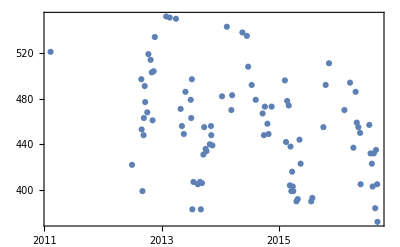

```mathematica
DateListPlot[dd],Joined->False]
```

Histogram of all ride durations 2011-2016:

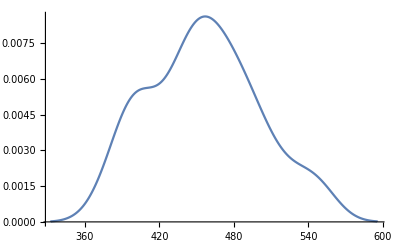

```mathematica
SmoothHistogram[durations]
```

Even overall the distribution seems to resemble normal. We need to clear data little more:

1. I know that I started riding regularly in second half of 2012, so data before that is some kind of error
2. There is seems to be a seasonal component which could be explained that I usually ride more catiously on wet road. We will ignore it for now.
3. Finally, it looks like the results change as I get more in shape, so we will need to look at it by year.